```mathematica
Steffemsem[p0_,cifras_]:=Method[{},P0=N[p0];e=10^(-N[cifras]);n=0;
P1=N[f[P0]];
P2=N[f[P1]];
p=N[P0-(P1-P0)^2/(P2-2*P1+P0)];
error=Abs[p-P0];
vector={{n,P0,P1,P2,p,error}};
While[  Abs[p-P0]>e&&n≤20,
P0=N[p];
P1=N[f[P0]];
P2=N[f[P1]];
p=N[P0-(P1-P0)^2/(P2-2*P1+P0)];
error=Abs[p-P0];
n=n+1;
 vector=Append[vector,{n,P0,P1,P2,p,error}]
];Print[NumberForm[TableForm[vector,TableHeadings->{None, {"n","P{0}","P{1}","P{2}","P","e_a"}}],16]];];
```

```mathematica
f[x_]:=x^3- 1;
```

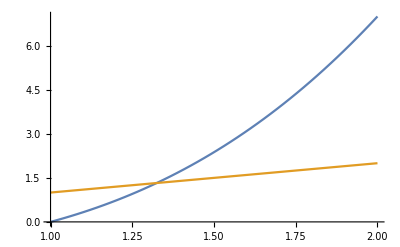

```mathematica
Plot[{f[x],x},{x,1,2}]
```

```mathematica
Steffemsem[1.3,5]
```

n | P{0} | P{1} | P{2} | P | e_a
0 | 1.3 | 1.197 | 0.7150723730000021 | 1.327997430760043 | 0.02799743076004302
1 | 1.327997430760043 | 1.342025958814858 | 1.417033943386103 | 1.324770120931007 | 0.00322730982903563
2 | 1.324770120931007 | 1.324992590722788 | 1.326164101481298 | 1.324717970591887 | 0.00005215033912087108
3 | 1.324717970591887 | 1.324718027512543 | 1.32471832717893 | 1.324717957244747 | 1.334713961576028×10^-8

```mathematica
Method[{},Null]
```

```mathematica
f[x_]:=2^-x;
```

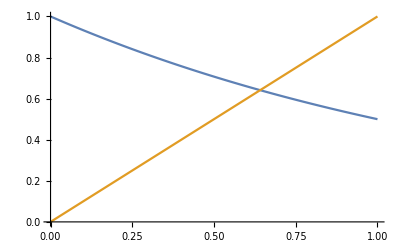

```mathematica
Plot[{f[x],x},{x,0,1}]
```

```mathematica
Steffemsem[0.5,5]
```

n | P{0} | P{1} | P{2} | P | e_a
0 | 0.5 | 0.7071067811865476 | 0.6125473265360659 | 0.6421876687473401 | 0.1421876687473401
1 | 0.6421876687473401 | 0.6407406077985924 | 0.6413836098463808 | 0.6411857920609144 | 0.001001876686425707
2 | 0.6411857920609144 | 0.6411857233694153 | 0.6411857538983964 | 0.6411857445049861 | 4.755592830640865×10^-8

Method[{},Null]

```mathematica
f[x_]:=2+Sin[x];
```

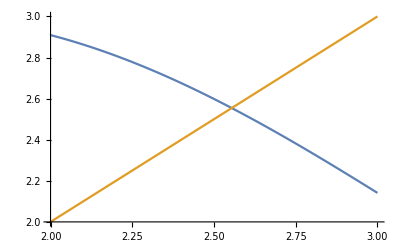

```mathematica
Plot[{f[x],x},{x,2,3}]
```

```mathematica
Steffemsem[2.4,5]
```

n | P{0} | P{1} | P{2} | P | e_a
0 | 2.4 | 2.675463180551151 | 2.449432062562147 | 2.551307729839086 | 0.1513077298390866
1 | 2.551307729839086 | 2.556597755061361 | 2.55219512916454 | 2.554194903483165 | 0.002887173644078533
2 | 2.554194903483165 | 2.554196826304463 | 2.554195225774574 | 2.554195952836904 | 1.049353739457359×10^-6

Method[{},Null]

```mathematica
f[x_]:=(x^3-5)/2;
```

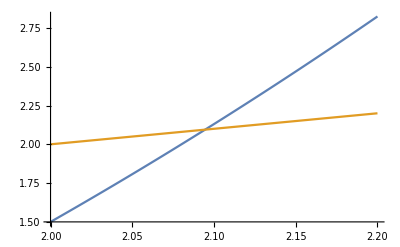

```mathematica
Plot[{f[x],x},{x,2,2.2}]
```

```mathematica
Steffemsem[2,5]
```

n | P{0} | P{1} | P{2} | P | e_a
0 | 2. | 1.5 | -0.8125 | 2.137931034482758 | 0.1379310344827585
1 | 2.137931034482758 | 2.385973184632415 | 4.29151524090292 | 2.100811932379848 | 0.0371191021029107
2 | 2.100811932379848 | 2.135873009548016 | 2.371876689524698 | 2.09469436888156 | 0.006117563498287293
3 | 2.09469436888156 | 2.095491847098432 | 2.100742541589676 | 2.094551557154664 | 0.0001428117268962303
4 | 2.094551557154664 | 2.094551979125881 | 2.094554756000587 | 2.094551481542348 | 7.561231640806909×10^-8

Method[{},Null]

```mathematica
f[x_]:=√E^x/3;
```

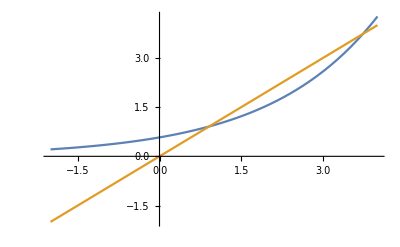

```mathematica
Plot[{f[x],x},{x,-2,4}]
```

```mathematica
Steffemsem[3,5]
```

n | P{0} | P{1} | P{2} | P | e_a
0 | 3. | 2.587504391183885 | 2.105274897528294 | 5.44002793884578 | 2.44002793884578
1 | 5.44002793884578 | 8.76448556845955 | 46.19800613455685 | 5.116007940064875 | 0.324019998780904
2 | 5.116007940064875 | 7.453605132135597 | 23.98662592101885 | 4.731069752408122 | 0.3849381876567533
3 | 4.731069752408122 | 6.148626551202784 | 12.49098433983783 | 4.323039604194133 | 0.4080301482139888
4 | 4.323039604194133 | 5.013898006384307 | 7.082612656101094 | 3.976642559703074 | 0.3463970444910598
5 | 3.976642559703074 | 4.216541049871997 | 4.753895468599617 | 3.783164198507889 | 0.1934783611951851
6 | 3.783164198507889 | 3.827745374996859 | 3.914026122868753 | 3.735502286617 | 0.04766191189088875
7 | 3.735502286617 | 3.737604876684357 | 3.741536268293217 | 3.733084919346128 | 0.002417367270871829
8 | 3.733084919346128 | 3.733090023898174 | 3.733099551786494 | 3.733079028667693 | 5.89067843526081×10^-6

Method[{},Null]

```mathematica
f[x_]:=Cos[x];
```

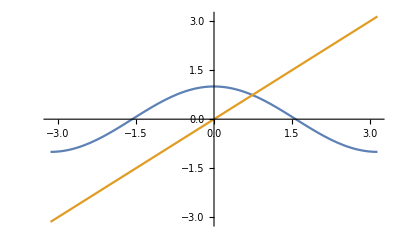

```mathematica
Plot[{f[x],x},{x,-Pi,Pi}]
```

```mathematica
Steffemsem[0.6,5]
```

n | P{0} | P{1} | P{2} | P | e_a
0 | 0.6 | 0.825335614909678 | 0.6783104022254399 | 0.7363627309425187 | 0.1363627309425187
1 | 0.7363627309425187 | 0.7409162350155599 | 0.7378504426536159 | 0.7390840319865361 | 0.002721301044017355
2 | 0.7390840319865361 | 0.7390858750155608 | 0.7390846335292844 | 0.7390851332149802 | 1.101228444211344×10^-6

Method[{},Null]